Exercises for Section 18 | Geocomputation

Find the distance from New York to London. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]
```

3453.71 mi

```mathematica
GeoGraphics[GeoPath[{Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]}]]
```

-Graphics-

Divide the distance from New York to London by the distance from New York to San Francisco. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]/GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]]
```

1.3511

Find the distance from Sydney to Moscow in kilometers. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[GeoDistance[Entity["City",{"Sydney","NewSouthWales","Australia"}],Entity["City",{"Moscow","Moscow","Russia"}]],"Km"]
```

14462. km

Generate a map of the United States. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoGraphics[Entity["Country","UnitedStates"]]
```

-Graphics-

Plot on a map Brazil, Russia, India and China. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoListPlot[{Entity["Country","Brazil"],Entity["Country","Russia"],Entity["Country","India"],Entity["Country","China"]}]
```

-Graphics-

Plot on a map the path from New York City to Beijing. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoGraphics[GeoPath[{Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Beijing","Beijing","China"}]}]]
```

-Graphics-

Plot a disk centered on the Great Pyramid, with radius 10 miles. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoGraphics[GeoDisk[Entity["Building","GreatPyramidOfGiza::jbm66"],10 Quantity[, "Miles"]]]
```

-Graphics-

Plot a disk centered on New York with a radius large enough to just reach San Francisco. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoGraphics[GeoDisk[Entity["City",{"NewYork","NewYork","UnitedStates"}],GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]]]]
```

-Graphics-

Find the nearest 5 countries to the North Pole (GeoPosition["NorthPole"]). |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoNearest["Country",GeoPosition["NorthPole"],5]
```

{Greenland,Canada,Russia,Svalbard,United States}

Find the flags of the 3 countries nearest to latitude 45°, longitude 0°. |

EXPECTED OUTPUT »

-Graphics- | ×


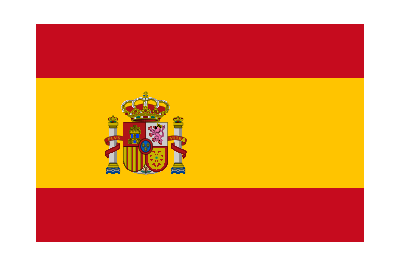
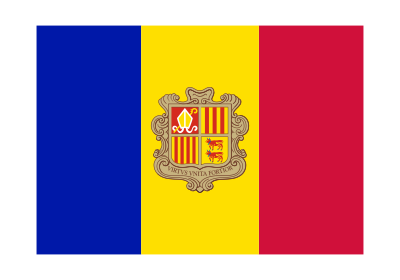

```mathematica
EntityValue[GeoNearest["Country",GeoPosition[{45, 0}],3],"Flag"]
```

Plot the 25 volcanoes closest to Rome. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoListPlot[GeoNearest["Volcano",Entity["City",{"Rome","Lazio","Italy"}],25]]
```

-Graphics-

Find the difference in latitude between New York and Los Angeles. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Entity["City",{"NewYork","NewYork","UnitedStates"}][EntityProperty["City","Latitude"]]-EntityValue[Entity["City",{"LosAngeles","California","UnitedStates"}],"Latitude"]
GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]][[1, 1]] - GeoPosition[Entity["City",{"LosAngeles","California","UnitedStates"}]][[1, 1]]
```

6.64488 °

6.64488

```mathematica
Entity["NewYorkCity"]
```

Entity[NewYorkCity]

```mathematica
InputForm[Entity["City",{"NewYork","NewYork","UnitedStates"}]]
```

"Entity[\"City\", {\"NewYork\", \"NewYork\", \"UnitedStates\"}]"

```mathematica
First[GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]]
```

{40.6643,-73.9385}

```mathematica
EntityValue[Entity["City",{"NewYork","NewYork","UnitedStates"}],"Latitude"]
EntityValue[Entity["City",{"LosAngeles","California","UnitedStates"}],"Latitude"]
```

40.6643 °

34.0194 °

```mathematica
GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]
First[First[GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]]]
First[GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]][[1]]-First[GeoPosition[Entity["City",{"LosAngeles","California","UnitedStates"}]]][[1]]
```

GeoPosition[{40.6643,-73.9385}]

40.6643

40.6643

```mathematica
First[GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]][[1]]-First[GeoPosition[Entity["City",{"LosAngeles","California","UnitedStates"}]]][[1]]
```

6.64488

Plot on a map the countries in NATO. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoListPlot[EntityClass["Country","NATO"]]
```

-Graphics-

Plot on a map a thick red line from Moscow to Beijing and a thick blue line from Washington, DC to London. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoGraphics[{Style[GeoPath[{Entity["City",{"Moscow","Moscow","Russia"}],Entity["City",{"Beijing","Beijing","China"}]}],Thick,Red],Style[GeoPath[{Entity["AdministrativeDivision",{"DistrictOfColumbia","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]}],Thick,Blue]}]
```

-Graphics-

Find the distance from 0 latitude, 0 longitude to the Eiffel Tower. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoDistance[GeoPosition[{0,0}],GeoPosition[Entity["Building","EiffelTower::5h9w8"]]]
GeoDistance[GeoPosition[{0, 0}],Entity["Building","EiffelTower::5h9w8"]]
```

3366.82 mi

3366.82 mi

```mathematica
Entity["Building", "EiffelTower::5h9w8"]
```

Eiffel Tower

```mathematica
Entity["Building","EiffelTower::5h9w8"]
```

```mathematica
GeoDistance[GeoPosition[{0, 0}],Entity["Building","EiffelTower::5h9w8"]]
```

3366.82 mi

Plot a disk styled red of radius 100 miles centered on Los Angeles. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoGraphics[{Red,GeoDisk[Entity["City",{"LosAngeles","California","UnitedStates"}],100 Quantity[, "Miles"]]}]
```

-Graphics-

Make a list of plots showing disks with radii 1, 2 and 3 miles around the Empire State Building. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoGraphics[Table[GeoDisk[Entity["Building","EmpireStateBuilding::h583b"],r],{r,{1 Quantity[, "Miles"],2 Quantity[, "Miles"],3 Quantity[, "Miles"]}}]]
GeoGraphics[
```

-Graphics-

```mathematica
Table[GeoGraphics[GeoDisk[Entity["Building","EmpireStateBuilding::h583b"],r]],{r,{1 Quantity[, "Miles"],2 Quantity[, "Miles"],3 Quantity[, "Miles"]}}]
```

{-Graphics-,-Graphics-,-Graphics-}

Find the 5 countries nearest to New York City. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoNearest["Country",Entity["City",{"NewYork","NewYork","UnitedStates"}],5]
```

{United States,Canada,Bermuda,Bahamas,Saint Pierre and Miquelon}

Find the nearest ocean to Chicago. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GeoNearest["Ocean",Entity["City",{"Chicago","Illinois","UnitedStates"}]]
```

{Atlantic Ocean}